This notebook generates plots for the Rail preprint. Enter the directory where “perform” files may be found below.

```mathematica
SetDirectory["/Users/eterna/results_v2"];
```

```mathematica
(*Plot number of reads in GEUVADIS samples. geuvadis_read_counts was obtained by wc -l ing the _1.fastq.gz GEUVADIS files and dividing all results by 2.*)
```

```mathematica
geuvadisReadCounts = ReadList[NotebookDirectory[] <>"geuvadis_read_counts"];
```

```mathematica
Median[geuvadisReadCounts]
```

52609404

```mathematica
MedianDeviation[geuvadisReadCounts]
```

12553184

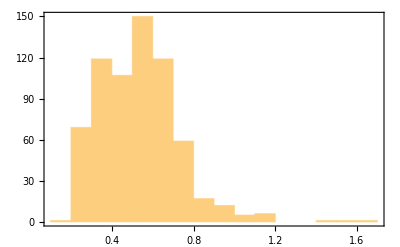

```mathematica
Histogram[ReadList["/Users/eterna/pv2/geuvadis_read_counts"], ImageSize->Full,  Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Plot histogram of incidence of exon-exon junctions across samples. intron_histogram is generated by intron_histogram.py*)
```

```mathematica
intronHistogram = Import[NotebookDirectory[] <>"intron_histogram", "TSV"];
```

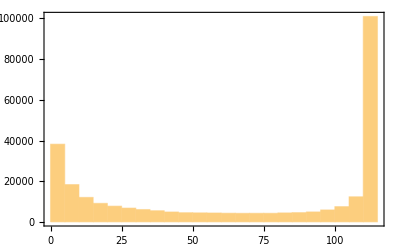

```mathematica
Histogram[Transpose[intronHistogram][[2]],ImageSize->Full,  Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Select sample*)
```

```mathematica
sampleName="NA20768_female_TSI_HMGU_5-1-1"
```

NA20768_female_TSI_HMGU_5-1-1

```mathematica
FileNames["harvest/*noann*perform_true"]~Join~FileNames["harvest/*rail*perform_true"]~Join~FileNames["harvest/*withfilter*perform_true"]
```

{harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_noann_paired_1pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_noann_paired_2pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_star_noann_paired_1pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_star_nogen_noann_paired_2pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_tophat_noann_paired_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_rail_perform_true,harvest/withfilter_NA20768_female_TSI_HMGU_5-1-1_perform_true}

```mathematica
allTrueStatsFiles=FileNames["harvest/*noann*perform_true"]~Join~FileNames["harvest/*subjunc*perform_true"]~Join~FileNames["harvest/*rail*perform_true"]~Join~FileNames["harvest/*withfilter*perform_true"]
```

{harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_noann_paired_1pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_noann_paired_2pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_star_noann_paired_1pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_star_nogen_noann_paired_2pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_tophat_noann_paired_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_subjunc_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_rail_perform_true,harvest/withfilter_NA20768_female_TSI_HMGU_5-1-1_perform_true}

```mathematica
allTrueStats = Import[#, "TSV"]&/@allTrueStatsFiles;
```

```mathematica
accumulated=Accumulate/@Transpose/@Transpose/@allTrueStats;
```

```mathematica
(*Plot of coverage bias correction vs. protocols using no annotation (Figure 5)*)
```

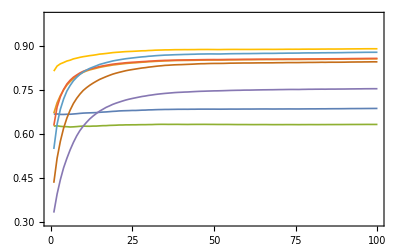

```mathematica
ListPlot[Table[N[#[[4]]]/#[[2]]&/@accumulated[[i]], {i, 1, Length[allTrueStats]}], Joined->True, PlotStyle->Thickness[.003], PlotRange->{All, {0.3, 1}}, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Get color matchups for constructing legend in Keynote*)
```

```mathematica
Transpose[{allTrueStatsFiles, ColorData[97,"ColorList"][[Range[1,8]]]}]
```

{{harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_noann_paired_1pass_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_noann_paired_2pass_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_star_noann_paired_1pass_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_star_nogen_noann_paired_2pass_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_tophat_noann_paired_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_subjunc_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_rail_perform_true,-Graphics-},{harvest/withfilter_NA20768_female_TSI_HMGU_5-1-1_perform_true,-Graphics-}}

```mathematica
allTrueStatsFilesAnn={"harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_ann_paired_1pass_perform_true","harvest/NA20768_female_TSI_HMGU_5-1-1_star_ann_paired_1pass_perform_true","harvest/NA20768_female_TSI_HMGU_5-1-1_tophat_ann_paired_perform_true","harvest/withfilter_NA20768_female_TSI_HMGU_5-1-1_perform_true"}
```

{harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_ann_paired_1pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_star_ann_paired_1pass_perform_true,harvest/NA20768_female_TSI_HMGU_5-1-1_tophat_ann_paired_perform_true,harvest/withfilter_NA20768_female_TSI_HMGU_5-1-1_perform_true}

```mathematica
allTrueStats = Import[#, "TSV"]&/@allTrueStatsFilesAnn;
```

```mathematica
accumulated=Accumulate/@Transpose/@Transpose/@allTrueStats;
```

```mathematica
(*Plot of coverage bias correction vs. protocols using annotation (Figure 6)*)
```

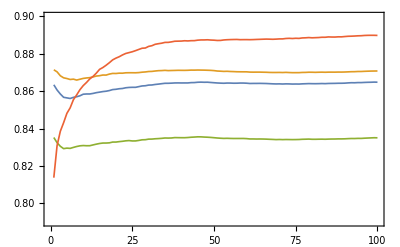

```mathematica
ListPlot[Table[N[#[[4]]]/#[[2]]&/@accumulated[[i]], {i, 1, Length[allTrueStats]}], Joined->True, PlotStyle->Thickness[.003], PlotRange->{{0, 100}, {0.79, 0.90}}, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Get color matchups for constructing legend in Keynote*)
```

```mathematica
Transpose[{allTrueStatsFilesAnn, ColorData[97,"ColorList"][[Range[1,4]]]}]
```

{{harvest/NA20768_female_TSI_HMGU_5-1-1_hisat_ann_paired_1pass_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_star_ann_paired_1pass_perform_true,-Graphics-},{harvest/NA20768_female_TSI_HMGU_5-1-1_tophat_ann_paired_perform_true,-Graphics-},{harvest/withfilter_NA20768_female_TSI_HMGU_5-1-1_perform_true,-Graphics-}}

```mathematica
(*Plot scaling with respect to number of samples (Figure 1c)*)
```

```mathematica
data={{28, 315/60},{28, 321/60},{28, 315/60}, {56, 459/60}, {112, 754/60}}
```

{{28,21/4},{28,107/20},{28,21/4},{56,153/20},{112,377/30}}

```mathematica
data //N
```

{{28.,5.25},{28.,5.35},{28.,5.25},{56.,7.65},{112.,12.5667}}

```mathematica
(*Get mean starting point from 3 replicates of 28 experiment*)
```

```mathematica
mean28 ={28,(21/4*2+107/20)/3}
```

{28,317/60}

```mathematica
mean28 //N
```

{28.,5.28333}

```mathematica
LineBoundaries[x_]:={{x[[1]]-4, x[[2]]},{x[[1]]+4, x[[2]]}}
```

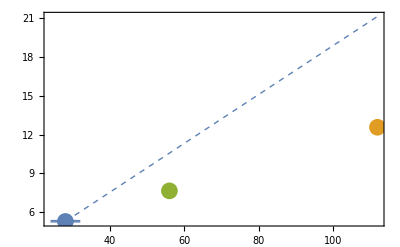

```mathematica
scaling=Show[ListPlot[data,PlotStyle->{White, Thick}], Graphics[{Thick,ColorData[97,"ColorList"][[1]], Line[LineBoundaries[data[[1]]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[1]], Point[mean28]}],Graphics[{Thick,ColorData[97,"ColorList"][[1]], Line[LineBoundaries[data[[2]]]]}],Graphics[{PointSize[.03],ColorData[97,"ColorList"][[3]], Point[data[[4]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[2]], Point[data[[5]]]}],
ListPlot[{mean28, mean28*2, mean28*4}, Joined->True, PlotStyle->{ColorData[97,"ColorList"][[1]], Dashing[.01], Thickness->0.0025}],
(*ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],*)
PlotRange->All, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Plot scaling with respect to number of instances (Figure 1a)*)
```

```mathematica
data={{40, 28/(315/60)},{40, 28/(321/60)},{40, 28/(315/60)},{10,28/(917/60)}, {20,28/(543/60)}}//N
```

{{40.,5.33333},{40.,5.23364},{40.,5.33333},{10.,1.83206},{20.,3.09392}}

```mathematica
mean40 ={40,(28/(315/60)*2+ 28/(321/60))/3}
```

{40,5104/963}

```mathematica
mean40 //N
```

{40.,5.3001}

```mathematica
LineBoundaries[x_]:={{x[[1]]-2, x[[2]]},{x[[1]]+2, x[[2]]}}
```

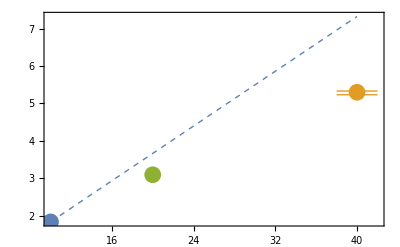

```mathematica
scaling=Show[ListPlot[data,PlotStyle->{White, Thick}],  Graphics[{Thick,ColorData[97,"ColorList"][[2]], Line[LineBoundaries[data[[1]]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[2]], Point[mean40]}],Graphics[{Thick,ColorData[97,"ColorList"][[2]], Line[LineBoundaries[data[[2]]]]}],Graphics[{PointSize[.03],ColorData[97,"ColorList"][[1]], Point[data[[4]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[3]], Point[data[[5]]]}],
ListPlot[{data[[4]], data[[4]]*2, data[[4]]*4}, Joined->True, PlotStyle->{ColorData[97,"ColorList"][[1]], Dashing[.01], Thickness->0.0025}],
(*ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],*)
PlotRange->All, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```